```mathematica
Needs["GraphUtilities`"]
```

```mathematica
g={1->19,1->15,1->36,1->23,1->18,1->39,2->36,2->23,2->4,2->18,2->26,2->9,3->35,3->6,3->16,3->11,4->23,4->2,4->18,4->24,5->14,5->8,5->29,5->21,6->34,6->35,6->3,6->16,7->30,7->33,7->38,7->28,8->12,8->14,8->5,8->29,8->31,9->39,9->13,9->20,9->10,9->17,9->2,10->9,10->20,10->12,10->14,10->29,11->3,11->16,11->30,11->33,11->26,12->20,12->10,12->14,12->8,13->24,13->39,13->9,13->20,14->10,14->12,14->8,14->5,15->26,15->19,15->1,15->36,16->6,16->3,16->11,16->30,16->17,16->35,16->32,17->38,17->28,17->32,17->40,17->9,17->16,18->2,18->4,18->24,18->39,18->1,19->27,19->26,19->15,19->1,20->13,20->9,20->10,20->12,21->5,21->29,21->25,21->37,22->32,22->40,22->34,22->35,23->1,23->36,23->2,23->4,24->4,24->18,24->39,24->13,25->29,25->21,25->37,25->31,26->31,26->27,26->19,26->15,26->11,26->2,27->37,27->31,27->26,27->19,27->29,28->7,28->38,28->17,28->32,29->8,29->5,29->21,29->25,29->10,29->27,30->16,30->11,30->33,30->7,30->37,31->25,31->37,31->27,31->26,31->8,32->28,32->17,32->40,32->22,32->16,33->11,33->30,33->7,33->38,34->40,34->22,34->35,34->6,35->22,35->34,35->6,35->3,35->16,36->15,36->1,36->23,36->2,37->21,37->25,37->31,37->27,37->30,38->33,38->7,38->28,38->17,38->40,39->18,39->24,39->13,39->9,39->1,40->17,40->32,40->22,40->34,40->38}
```

{1→19,1→15,1→36,1→23,1→18,1→39,2→36,2→23,2→4,2→18,2→26,2→9,3→35,3→6,3→16,3→11,4→23,4→2,4→18,4→24,5→14,5→8,5→29,5→21,6→34,6→35,6→3,6→16,7→30,7→33,7→38,7→28,8→12,8→14,8→5,8→29,8→31,9→39,9→13,9→20,9→10,9→17,9→2,10→9,10→20,10→12,10→14,10→29,11→3,11→16,11→30,11→33,11→26,12→20,12→10,12→14,12→8,13→24,13→39,13→9,13→20,14→10,14→12,14→8,14→5,15→26,15→19,15→1,15→36,16→6,16→3,16→11,16→30,16→17,16→35,16→32,17→38,17→28,17→32,17→40,17→9,17→16,18→2,18→4,18→24,18→39,18→1,19→27,19→26,19→15,19→1,20→13,20→9,20→10,20→12,21→5,21→29,21→25,21→37,22→32,22→40,22→34,22→35,23→1,23→36,23→2,23→4,24→4,24→18,24→39,24→13,25→29,25→21,25→37,25→31,26→31,26→27,26→19,26→15,26→11,26→2,27→37,27→31,27→26,27→19,27→29,28→7,28→38,28→17,28→32,29→8,29→5,29→21,29→25,29→10,29→27,30→16,30→11,30→33,30→7,30→37,31→25,31→37,31→27,31→26,31→8,32→28,32→17,32→40,32→22,32→16,33→11,33→30,33→7,33→38,34→40,34→22,34→35,34→6,35→22,35→34,35→6,35→3,35→16,36→15,36→1,36→23,36→2,37→21,37→25,37→31,37→27,37→30,38→33,38→7,38→28,38→17,38→40,39→18,39→24,39→13,39→9,39→1,40→17,40→32,40→22,40→34,40→38}

```mathematica
GraphPlot[g,VertexLabeling->True]
```

```mathematica
c=MinCut[g,2]
```

{{1,19,15,36,23,18,39,2,4,26,24,5,8,29,21,31,13,27,25,37},{9,3,35,6,16,11,14,34,7,30,33,38,28,12,20,10,17,32,40,22}}

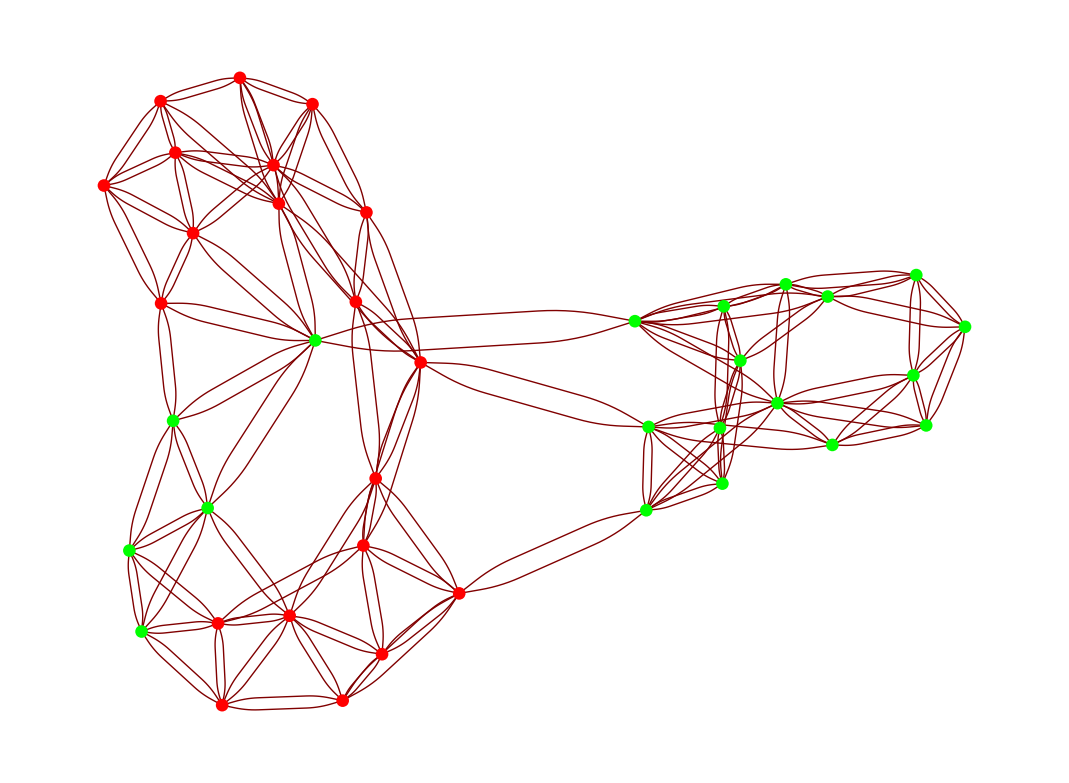

```mathematica
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c[[1]],#2],Red,Green],Disk[#1,.05]}&)]
```

```mathematica
?MinCut
```

MinCut[g,k] partitions the undirected graph g into k parts where the number of edge cuts is approximately minimized.